215

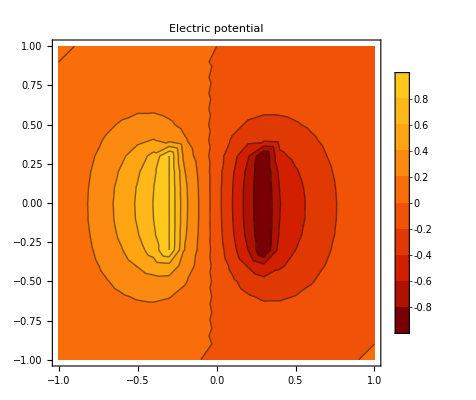

-Graphics3D-

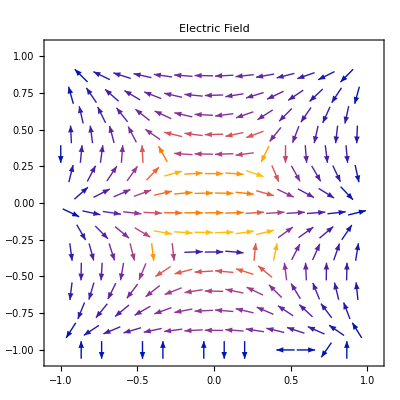

```mathematica
dx = 0.1;
xL = Range[-1,1,dx];
lx=Length[Range[-1,1,dx]];
v = Table[0,{i,lx},{j,lx}];
v[[1]]=0*xL;
v[[lx]] = 0*xL;
v[[All,1]]=0;
v[[All,-1]]=0;
Do[v[[m,n]]=1,{m,8,14},{n,8,14}];
tol = 0.00000001;
cond = 0;
vo = v;
counter = 0;
While[cond==0, Do[
Do[v[[i,j]]=0.25(v[[i+1,j]]+v[[i-1,j]]+v[[i,j+1]]+v[[i,j-1]]),{i,2,lx-1}]
,{j,2,lx-1}]; 
Do[v[[m,8]]=1,{m,8,lx-7}];Do[v[[m,14]]=-1,{m,8,lx-7}];
dv = Abs[v-vo];
If[Max[dv]< tol,cond = 1]; vo = v;counter++];
counter 
p1 =ListContourPlot[v,DataRange->{{-1,1},{-1,1}},ColorFunction->"SolarColors",PlotLegends->Automatic,PlotLabel->"Electric potential"]
potential={};
Do[Do[ AppendTo[potential,{i,j,v[[i,j]]}],{i,1,lx}],{j,1,lx}]
ListPlot3D[potential, Mesh->All,PlotLabel->"perspective plot of potential"]

Ex=Table[0,{i,lx},{j,lx}];
Do[Do[Ex[[i,j]]=-(v[[i+1,j]]-v[[i-1,j]])/(2*dx),{i,2,lx-1}],{j,2,lx-1}]
Ey=Table[0,{i,lx},{j,lx}];
Do[Do[Ey[[i,j]]=-(v[[i,j+1]]-v[[i,j-1]])/(2*dx),{i,2,lx-1}],{j,2,lx-1}]
ListVectorPlot[Table[{Ey[[i,j]],Ex[[i,j]]},{i,1,lx,1},{j,1,lx,1}],DataRange->{{-1,1},{-1,1}},PlotLabel->"Electric Field"]
```